# Project 2 Hiking

## Defining the Mountain Range

Assign values to parameters

```mathematica
Subscript[C, 1]={1,1}; Subscript[C, 2]={3,1}; Subscript[C, 3]={3.75,1}; Subscript[C, 4]={4,3}; Subscript[C, 5]={3,3.5}; Subscript[C, 6]={2,3};  Subscript[C, 7]={0.75,3};
Subscript[ϵ, 1]=1;Subscript[ϵ, 2]=√3;Subscript[ϵ, 3]=√2;Subscript[ϵ, 4]=√2;Subscript[ϵ, 5]=√3;Subscript[ϵ, 6]=√2;Subscript[ϵ, 7]=2;
Subscript[λ, 1]=1;Subscript[λ, 2]=1;Subscript[λ, 3]=0.8;Subscript[λ, 4]=1;Subscript[λ, 5]=0.75;Subscript[λ, 6]=1;Subscript[λ, 7]=0.5;
```

```mathematica
mag[u_]=Sqrt[u.u];
```

```mathematica
m[x_,y_]=7+Sum[Subscript[λ, i]*Exp[-Subscript[ϵ, i]^2*(mag[{x,y}-Subscript[C, i]])^2],{i,7}];

mountain=Plot3D[m[x,y],{x,0,5},{y,0,5},AxesLabel->{Style["x",Medium],Style["y",Medium],Style["elevation"]},PlotLabel->Style["Elevation of the Lagrange Mountain", Bold], ImageSize->Large]
topo=ContourPlot[m[x,y],{x,0,5},{y,0,5},FrameLabel->{Style["x",Medium, Bold],Style["y",Medium, Bold]},Contours->35,ContourLabels->True, ImageSize->Large, PlotTheme->"Detailed"]
(* {7.050,7.100,7.150,7.200,7.250,7.300,7.350,7.400,7.450,7.500,7.550,7.600,7.650,7.700,7.750,7.800,7.850,7.900,7.950,8.000,8.050,8.100,8.150,8.200,8.250,8.300,8.350,8.400,8.450} *)
```

-Graphics3D-

-Graphics-

```mathematica
Analyzing the Mountain Range
```

### The Graph of the Trail

The trail that we will take

```mathematica
r[t_]={2.5+1.8Cos[4*t],2+1.2*Sin[4*t]};
a=r[t][[1]];b=r[t][[2]];
trail2D=ParametricPlot[r[t],{t,0,π/2}];
starting2D=Graphics[{{Green,Disk[r[0],0.1]},Text["Starting Point",{2.5+1.8*Cos[4*0]+0.1,2+1.2*Sin[4*0]+0.2}]}];
trail3D=ParametricPlot3D[{a,b,m[a,b]},{t,0,π/2}];
starting3D=Graphics3D[{{Green,Sphere[{r[0][[1]],r[0][[2]],m[r[0][[1]],r[0][[2]]]},0.1]},Text["Starting Point",{r[0][[1]],r[0][[2]],m[r[0][[1]],r[0][[2]]]}]}];
Show[topo,trail2D,starting2D]
Show[mountain,trail3D,starting3D]
```

-Graphics-

-Graphics3D-

### The direction of the trail

Since one of our friend cannot go down the steepest section of the trail, we need to choose the correct direction of the trail.
First, we need to analyze the rate chage of the mountain along the trail that we will take.

rate chage of elevation of counterclock wise

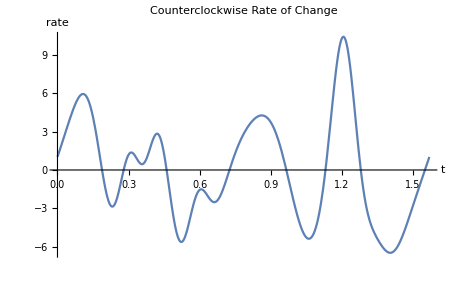

```mathematica
mt[t_]=m[a,b];
rate[t_]=mt'[t];
ccrate = Plot[rate[t],{t,0,π/2},AxesLabel->{Style["t",Medium, Bold],Style["rate",Medium, Bold]}, PlotLabel->Style["Counterclockwise Rate of Change", Medium, Bold, Blue]]
```

(* rate change of elevation of clockwise *)
 crate = Plot[-rate[-t],{t,0,π/2}, AxesLabel→{Style["t",Medium, Bold],Style["rate",Medium, Bold]}, PlotLabel→Style["Clockwise Rate of Change", Medium, Bold, Blue]]

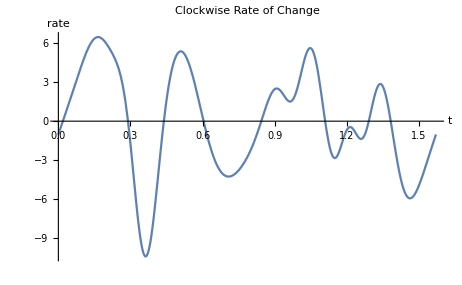

### The Angry Badger

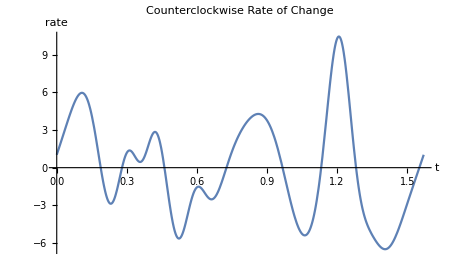

```mathematica
(*rate of change*)
ccrate
```

slope of the mouantain along the trail that we take

```mathematica
unidriction[t_]=r'[t]/mag[r'[t]];
```

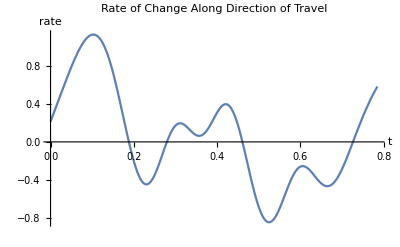

```mathematica
gradient[x_,y_]={D[m[x,y],x],D[m[x,y],y]};
gradientoft[t_]=gradient[a,b];
slope[t_] = gradientoft[t].unidriction[t];
 slopeplot =Plot[slope[t],{t,0,π/4},AxesLabel->{Style["t",Medium, Bold],Style["rate",Medium, Bold]}, PlotLabel->Style["Rate of Change Along Direction of Travel", Medium, Bold, Blue]]
```

```mathematica
rate[π/4](* rate of change when t = π/4 *)
```

2.79105

```mathematica
slope[π/4] (* slope when t = π/4 *)
```

0.581468

### Maximum and Minimum Change in Elevation

```mathematica
maximum=FindMaximum[rate[t],{t,1.2}];
"The maximum rate of change is: "
maximum[[1]] 
"at t =" 
t/.maximum[[2]]
```

The maximum rate of change is:

10.4295

at t =

1.20765

```mathematica
minimum=FindMinimum[rate[t],{t,1.4}];
"The maximum rate of change is: "
minimum[[1]] 
"at t =" 
t/.minimum[[2]]
```

The maximum rate of change is:

-6.48564

at t =

1.40558

### Maximum and Minimum Elevation Along the Trail

```mathematica
(*rewrite the parametric equation of r[t] in terms of x and y
((x-2.5)/1.8)^2+((y-2)/1.2)^2==1*)
rxy[x_,y_]=((x-2.5)/1.8)^2+((y-2)/1.2)^2;
deri[x_,y_]=D[rxy[x,y],{{x,y}}];
```

```mathematica
roots = FindRoot[{gradient[x,y]⟦1⟧==λ deri[x,y]⟦1⟧,gradient[x,y]⟦2⟧==λ deri[x,y]⟦2⟧,((x-2.5)/1.8)^2+((y-2)/1.2)^2==1},{x,3.1},{y,1},{λ,1}]
```

{x→3.22194,y→0.900748,λ→-0.444663}

```mathematica
"The maximum elevation on the trail is:"
m[x/.roots[[1]], y/.roots[[2]]]*1000
```

The maximum elevation on the trail is:

8293.75

### Lake Mochi

```mathematica
(*since tha lake must be located at the local mimimum point, according to our topo map, the local mimimum is aound point (3,2). There for, we use finding minimum function to find the exact point of the lake.*)
```

```mathematica
lakecoords = FindMinimum[m[x,y],{x,3},{y,2}]
```

{7.10818,{x→2.94776,y→2.13282}}

```mathematica
(*Therefore the coordinate of the Lake Mochi is (2.9477591758178754,2.1328212987045188)*)
```

```mathematica
LakeMochi=Graphics[{Blue,Disk[{x/.lakecoords[[2]][[1]],y/.lakecoords[[2]][[2]]},0.15],Text["Lake Mochi",{x/.lakecoords[[2]][[1]],0.2+y/.lakecoords[[2]][[2]]}]}];
Show[topo,LakeMochi]
```

-Graphics-

## Our Final Topo Map

```mathematica
Show[topo,trail2D,starting2D,LakeMochi]
```

-Graphics-

## Extra Credit

```mathematica
Subscript[ce, 1]={1,1.17}; Subscript[ce, 2]={1,3.228}; Subscript[ce, 3]={2,2.56}; Subscript[ce, 4]={2,4.436}; Subscript[ce, 5]={3,0.563}; Subscript[ce, 6]={3,4.46}; Subscript[ce, 7]={4,1.17}; Subscript[ce, 8]={4,3.8228}; Subscript[ce, 9]={4.3,3.6}; Subscript[ce, 10]={0.5,2.2}; 
Subscript[ce, 11]={2.5,2.5};

Subscript[ϵe, 1]=1; Subscript[ϵe, 2]=0.4; Subscript[ϵe, 3]=1; Subscript[ϵe, 4]=√2; Subscript[ϵe, 5]=√2; Subscript[ϵe, 6]=√2; Subscript[ϵe, 7]=1; Subscript[ϵe, 8]=1; Subscript[ϵe, 9]=√2; Subscript[ϵe, 10]=2 √2; Subscript[ϵe, 11]=1;
Subscript[λe, 1]=3.5; Subscript[λe, 2]=2; Subscript[λe, 3]=0.7; Subscript[λe, 4]=2; Subscript[λe, 5]=5; Subscript[λe, 6]=1; Subscript[λe, 7]=1.5; Subscript[λe, 8]=2.3; Subscript[λe, 9]=3.5; Subscript[λe, 10]=1; Subscript[λe, 11]=1;
```

```mathematica
M[x_,y_]=Sum[Subscript[λe, i]*Sin[Exp[-Subscript[ϵe, i]^2*(mag[{x,y}-Subscript[ce, i]])^2]],{i,10}]+Sin[-Subscript[ϵe, 11]^2*(mag[{x,y}-Subscript[ce, 11]])^2]*Cos[-Subscript[ϵe, 11]^2*(mag[{x,y}-Subscript[ce, 11]])^2];
erange =Plot3D[M[x,y],{x,0,5},{y,0,5}, ImageSize->Large, ColorFunction->"AlpineColors", AxesLabel->{Style["x",Bold, Medium],Style["y",Bold, Medium],Style["z",Bold, Medium]}, AspectRatio->1, PlotTheme->"Detailed",Lighting->{{"Point",RGBColor[1,1,0.79], {4.6,0,5.3}}}];
sun = Graphics3D[{Yellow, PointSize[0.05], Point[{4.6,0,5.3}]}];
(* The graph can appear to be changing shape when moving around the viewing angle because of the forced 1:1 aspect ratio to bring out the peaks. *)
```

```mathematica
Show[erange,sun] (* The sun is emulated to be in the corner of the rendered box for Point lighting. This was favored over directional lighting simply because it looks better. *)
```

-Graphics3D-